```mathematica
(*Smeared delta function*)
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.1;m=10;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
(*effective potential in oder of a^2*)
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
(*effective potential in order of a^4*)
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];
(*True potential -- Coulomb potentail*)
V[r_]=-α/r(*-1/r^0.01*);
```

```mathematica
(*Hydrogen atom wavefunction*)
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
(*Calculate all 20 states' energy with relativistic correction*)
EigenEnergyRela[V_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{(e-V )ϕ[r]+(e-V)^2/(8m)ϕ[r]+1/(2m)ϕ''[r]==0,ϕ'[max]==-min,ϕ[max]==min},ϕ,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[ϕ[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
(*Calculate single state's energy with relativistic correction*)
EigenEnergySoloRela[V_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{(e-V )ϕ[r]+(e-V)^2/(8m)ϕ[r]+1/(2m) ϕ''[r]==0,ϕ'[max]==-min,ϕ[max]==min},ϕ,{r,min,max},e,MaxSteps->steps,opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.
FindRoot[ϕ[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,ϕ[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},{opt___}]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{(ene-V )ϕ[r]+(ene-V)^2/(8m)ϕ[r]+1/(2m) ϕ''[r]==0,ϕ[r1]==r2,ϕ'[r1]==-r2},ϕ,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{(*ϕ'[r2]==1,*)ϕ[r2]==r2}}],2];
(*ϕ[rr]/.efunction*)
If[True,{amplitude=NIntegrate[ϕ[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude ϕ[rr]/.efunction},]
]
```

```mathematica
(*Coulomb eigenenergy without relativistic correction*)
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-0.05,-0.0125,-0.00555556,-0.003125,-0.002,-0.00138889,-0.00102041,-0.00078125,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195313,-0.00017301,-0.000154321,-0.000138504,-0.000125}

### Calculating eigen energy numerically adding a p^4 term as relativistic correction

```mathematica
EigenEnergySoloRela[V[r],{10^-15,4000},{-0.000124,-0.000125},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
eigennumer[[20]]=%;
```

ParametricNDSolve::precw: The precision of the differential equation ({{(e$31133+0.1 Power[«2»]) ϕ[r$31134]+1/80 (e$31133+Times[«2»])^2 ϕ[r$31134]+ϕ''[r$31134]/20==0,ϕ'[4000]==-1/1000000000000000,ϕ[4000]==1/1000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000125027734030949866574483510688,5.9530114961076112661893082977×10^34}time:7.4823231s

{-0.00012503083660005715836510904032,-1.7514150519867477827125304253×10^33}time:2.455079s

{-0.000125030747929192818299937507412,4.9612207848622619403245892965×10^30}time:2.358466s

{-0.000125030748179660637750398518371,4.122479174519481044194315631×10^26}time:2.203636s

{-0.000125030748179681451864909935126,1.446925852727415069518330135×10^23}time:2.015643s

{-0.000125030748179681452047609793868,-3.530530749106777657193553155×10^22}time:3.988951s

{-0.000125030748179681452011774514952,-3.2866582437503219844588999507×10^23}time:1.953143s

{-0.000125030748179681452051922492641,-6.0121289031726126852939001473×10^23}time:1.984595s

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

-0.000125030748179681452047609772848

```mathematica
AbsoluteTiming[eigennumer=EigenEnergyRela[V[r],{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]];
N[%,6]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(e$68418+0.1 Power[«2»]) ϕ[r$68419]+1/80 (e$68418+Times[«2»])^2 ϕ[r$68419]+ϕ''[r$68419]/20==0,ϕ'[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==-1/1000000000000000,ϕ[Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]]==1/1000000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{271.532,{-0.0501571,-0.0125255,-0.00556369,-0.00312855,-0.00200186,-0.00138998,-0.0010211,-0.000781717,-0.000617614,-0.000500241,-0.000413405,-0.000347363,-0.000295969,-0.000255191,-0.000222295,-0.000195372,-0.000173061,-0.00015437,-0.000138515,-0.000124016}}

```mathematica
Module[{n=20},First@First@Eigenfunsin[V[r],eigennumer[[n]],r,{800,1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-20}]]
```

NDSolve::precw: The precision of the differential equation ({{(-0.000124016428219064458886879024624+0.1 Power[«2»]) ϕ[r]+1/80 (-0.000124016428219064458886879024624+Times[«2»])^2 ϕ[r]+ϕ''[r]/20==0,ϕ[800]==1.×10^-50,ϕ'[800]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

1.00778×10^47                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 800.00000000000000000000000000000000000000000000000}}, <>][r]

```mathematica
NIntegrate[(%58)^2,{r,0,2000},WorkingPrecision->30]
```

NIntegrate::precw: The precision of the argument function (1.51897824512732×10^-591 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,800.}},«3»,{{{{1},{1},«47»,{49},«23943»},{«1»}}}][r])^2) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.1963857600388251944517724242053115011149743604018437196842592386697048874737741}. NIntegrate obtained 1.0000000000000815358296247341488044878055395181195242684928524917143310663936143 and 5.1393644889499952475882255510145066801832445637026746071243621141801876603419329×10^-7 for the integral and error estimates.

1.00000000000008153582962473415

```mathematica
Module[{n=20},First@Eigenfunsin[V[r],eigenKG[[n]],r,{800,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-50,Method->{"Shooting","StartingInitialConditions"->{ϕ'[r2]==1,ϕ[r2]==r2}}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {-5.1761×10^-44,Indeterminate} is not a list of numbers with dimensions {2} at {r,ϕ[r],ϕ'[r]} = {0.,2.70912×10^-42,-5.1761×10^-44}.

(WorkingPrecision→50)==(PrecisionGoal→15)==(InterpolationOrder→All)==(MaxSteps→∞)==(MaxStepFraction→1/10000)==(StartingStepSize→1/100000000000000000000000000000000000000000000000000)==(Method→{Shooting,StartingInitialConditions→{ϕ'[r2]==1,ϕ[r2]==r2}})==Normalization

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NLimit[First@((%58)/r),r->0,Scale->10]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

NLimit[3.89741×10^-296,r→0,Scale→10]

```mathematica
NIntegrate[(%185)^2,{r,0,800},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function (1.51897824512732×10^-591 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,800.}},«3»,{{{{1},{1},«47»,{49},«23943»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.487162366302553440145242034073569486623597778095375118241326515030867513609781154830789107053769278}. NIntegrate obtained 1.000000000000103698121685135138964374437879803117017783102792101995582757128485634213842069381132412 and 2.066878955972614088469005768860614644810097062490860912380481895499030938119397534699133560632255305×10^-17 for the integral and error estimates.

1.000000000000103698121685135138964374437879803117

```mathematica
NLimit[(%204)/r,r->0,WorkingPrecision->30,Scale->0.5]
```

-0.0506159

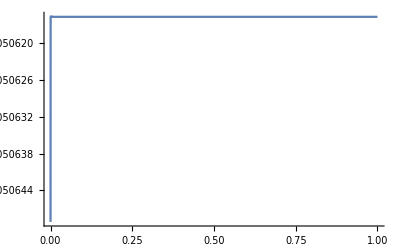

```mathematica
Plot[(%204)/r,{r,0,0.00000001},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
(*eigen energy from Klein-Gordon equation*)
eigenKG=Table[m/(√(1+α^2/((n-1/2+√(1/4-α^2))^2)))-m,{n,20}]
```

{-0.0506385,-0.0126034,-0.00558847,-0.00313937,-0.0020075,-0.00139329,-0.0010232,-0.000783135,-0.000618615,-0.000500974,-0.000413957,-0.000347789,-0.000296305,-0.000255461,-0.000222514,-0.000195554,-0.000173212,-0.000154491,-0.000138649,-0.000125124}

```mathematica
(*eigen energy from relativistic correction(perturbation).*)
eigenre=Table[-(m α^2)/(2 n^2)- 1/(2 m)NIntegrate[r^2((2 (m α)^(3/2))/n^(3/2) E^(-(m α r)/n)Hypergeometric1F1[1-n,2,(2 m α r)/n])^2 (-(m α^2)/(2 n^2)+α/r)^2,{r,0,∞}],{n,20}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {321.009}. NIntegrate obtained 3.98103×10^-6 and 5.53021×10^-12 for the integral and error estimates.

{-0.050625,-0.0126016,-0.00558796,-0.00313916,-0.0020074,-0.00139323,-0.00102317,-0.000783112,-0.000618599,-0.000500962,-0.000413949,-0.000347783,-0.0002963,-0.000255457,-0.000222511,-0.000195551,-0.000173209,-0.000154489,-0.000138647,-0.000125123}

```mathematica
(eigenKG-eigenre)/eigenKG
```

{0.000266002,0.000143573,0.0000911318,0.0000654067,0.0000505745,0.0000410503,0.0000344628,0.0000296546,0.0000260001,0.0000231334,0.0000208272,0.0000189334,0.0000173514,0.0000160108,0.0000148605,0.0000138631,0.0000129901,0.0000122198,0.0000115351,0.0000109227}

```mathematica
(*error of numerical calculation(comparing with perturbative result)*)
-(eigennumer-eigenKG)/eigenKG
```

{0.0095065,0.00617853,0.00443476,0.00344427,0.00281209,0.00237488,0.00205486,0.00181064,0.00161819,0.00146265,0.00133436,0.00122673,0.00113515,0.00105629,0.000987666,0.000927384,0.000871789,0.000782066,0.000963144,0.000745458}